-Graphics3D-

$Assumptions::bass: 0 不是一个格式良好的假设.

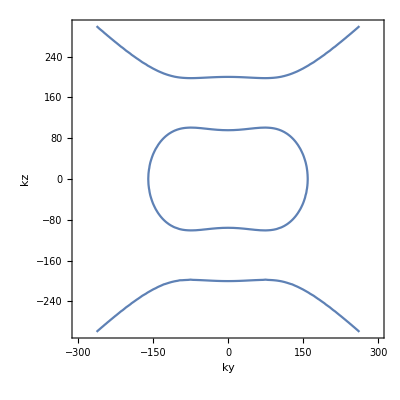

```mathematica
Clear["Global`*"]
m=DiagonalMatrix[List[1,1,1]] ;(*单位矩阵*)
μ=μr m;μr=0.5;
ϵ1=4;ϵ2=-3;
γr=0.5;c=3 10^8;ω=2*Pi 10^9 5;(*材料参数*)
ϵ=DiagonalMatrix[List[ϵ1,ϵ1,ϵ2]];
γ=γr m;
κ={{0,-kz,ky},{kz,0,-kx},{-ky,kx,0}};
M=κ.Inverse[μ].κ+I ω/c (κ.Inverse[μ].γ+γ.Inverse[μ].κ)+ω^2/c^2 (ϵ-γ.Inverse[μ].γ)//FullSimplify;(*波动方程*)
ContourPlot3D[Evaluate[Det[M]==0],{kx,-300,300},{ky,-300,300},{kz,-300,300},AxesLabel->{"kx","ky","kz"}]

Assuming[kx=0,ContourPlot[Evaluate[Det[M]==0],{ky,-300,300},{kz,-300,300},AxesLabel->{"ky","kz"}]]
```

```mathematica
Clear["Global`*"]
m=DiagonalMatrix[List[1,1,1]] ;(*单位矩阵*)
μ=μr m;(*材料参数*)
ϵ=DiagonalMatrix[List[ϵ1,ϵ1,ϵ2]];
μr=0.5;
ϵ1=4;ϵ2=-3;
γr=0.5;c=3 10^8;ω=2*Pi 10^9 5;
γ=γr m;
κ={{0,-kz,ky},{kz,0,-kx},{-ky,kx,0}};
M=(κ.Inverse[μ].κ+I ω/c (κ.Inverse[μ].γ+γ.Inverse[μ].κ)+ω^2/c^2 (ϵ-γ.Inverse[μ].γ)) c^2 μr//Simplify;(*波动方程*)
EE=List[Ex,Ey,Ez];
M1=M.EE;
aa=M1[[1]];
bb=M1[[2]];
cc=M1[[3]];
k=List[kx,ky,kz];
ky1=Sqrt[(ω/c)^2-kx^2-kz^2];
ky2=Sqrt[(ω/c)^2-kx^2-kz^2];
dd=k.ϵ.EE-γr^2/μr k.EE;
NSolve[Det[M]==0,ky]//FullSimplify;
ky=(√((c^2 (μr (2 kx^2 ϵ1+kz^2 (ϵ1+ϵ2))-2 γr^2 (kx^2+kz^2))+√μr √(c^4 kz^4 μr (ϵ1-ϵ2)^2+2 c^2 kz^2 ω^2 (ϵ1-ϵ2) (γr^2-μr ϵ1) (4 γr^2+μr (ϵ1-ϵ2))+ω^4 (γr^2-μr ϵ1)^2 (8 γr^2 (ϵ1+ϵ2)+μr (ϵ1-ϵ2)^2))+ω^2 (γr^2-μr ϵ1) (2 γr^2+μr (ϵ1+ϵ2)))/(c^2 (γr^2-μr ϵ1))))/(√2);
ky3=(√((c^2 (μr (2 kx^2 ϵ1+kz^2 (ϵ1+ϵ2))-2 γr^2 (kx^2+kz^2))-√μr √(c^4 kz^4 μr (ϵ1-ϵ2)^2+2 c^2 kz^2 ω^2 (ϵ1-ϵ2) (γr^2-μr ϵ1) (4 γr^2+μr (ϵ1-ϵ2))+ω^4 (γr^2-μr ϵ1)^2 (8 γr^2 (ϵ1+ϵ2)+μr (ϵ1-ϵ2)^2))+ω^2 (γr^2-μr ϵ1) (2 γr^2+μr (ϵ1+ϵ2)))/(c^2 (γr^2-μr ϵ1))))/(√2);
ky4=(√((c^2 (μr (2 kx^2 ϵ1+kz^2 (ϵ1+ϵ2))-2 γr^2 (kx^2+kz^2))+√μr √(c^4 kz^4 μr (ϵ1-ϵ2)^2+2 c^2 kz^2 ω^2 (ϵ1-ϵ2) (γr^2-μr ϵ1) (4 γr^2+μr (ϵ1-ϵ2))+ω^4 (γr^2-μr ϵ1)^2 (8 γr^2 (ϵ1+ϵ2)+μr (ϵ1-ϵ2)^2))+ω^2 (γr^2-μr ϵ1) (2 γr^2+μr (ϵ1+ϵ2)))/(c^2 (γr^2-μr ϵ1))))/(√2);
Ez=1;
(*Solve[{aa==0,bb==0,cc==0,dd==0},{Ex,Ey}]//FullSimplify;*)
Ex3=(c (c^3 kx (ϵ1-ϵ2) μr kz^3+c kx ((γr^2-ϵ1 μr) (4 γr^2+(ϵ1-ϵ2) μr) ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)) kz-2 ⅈ γr (γr^2-ϵ1 μr)^2 ω^3 √(1/(c^2 (γr^2-ϵ1 μr))(2 ((2 ϵ1 kx^2+kz^2 (ϵ1+ϵ2)) μr-2 (kx^2+kz^2) γr^2) c^2+2 (γr^2-ϵ1 μr) (2 γr^2+(ϵ1+ϵ2) μr) ω^2-2 √μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)))))/(c^4 (ϵ1-ϵ2) μr kz^4+c^2 (2 (γr^2-ϵ1 μr) (2 γr^2+(ϵ1-ϵ2) μr) ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)) kz^2-(γr^2-ϵ1 μr) ω^2 (4 ω^2 γr^4+(ϵ2-5 ϵ1) μr ω^2 γr^2+ϵ1 (ϵ1-ϵ2) μr^2 ω^2-√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)));
Ey3=(c (8 ⅈ kx γr (γr^2-ϵ1 μr)^2 ω^3+c kz √(1/(c^2 (γr^2-ϵ1 μr))(2 ((2 ϵ1 kx^2+kz^2 (ϵ1+ϵ2)) μr-2 (kx^2+kz^2) γr^2) c^2+2 (γr^2-ϵ1 μr) (2 γr^2+(ϵ1+ϵ2) μr) ω^2-2 √μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4))) (c^2 (ϵ1-ϵ2) μr kz^2+(γr^2-ϵ1 μr) (4 γr^2+(ϵ1-ϵ2) μr) ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4))))/(2 (c^4 (ϵ1-ϵ2) μr kz^4+c^2 (2 (γr^2-ϵ1 μr) (2 γr^2+(ϵ1-ϵ2) μr) ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)) kz^2-(γr^2-ϵ1 μr) ω^2 (4 ω^2 γr^4+(ϵ2-5 ϵ1) μr ω^2 γr^2+ϵ1 (ϵ1-ϵ2) μr^2 ω^2-√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4))));
Ex4=(c (c^3 kx (ϵ1-ϵ2) μr kz^3+c kx ((γr^2-ϵ1 μr) (4 γr^2+(ϵ1-ϵ2) μr) ω^2-√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)) kz-2 ⅈ √2 γr (γr^2-ϵ1 μr)^2 ω^3 √(1/(c^2 (γr^2-ϵ1 μr))(((2 ϵ1 kx^2+kz^2 (ϵ1+ϵ2)) μr-2 (kx^2+kz^2) γr^2) c^2+(γr^2-ϵ1 μr) (2 γr^2+(ϵ1+ϵ2) μr) ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)))))/(c^4 (ϵ1-ϵ2) μr kz^4+c^2 (2 (γr^2-ϵ1 μr) (2 γr^2+(ϵ1-ϵ2) μr) ω^2-√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)) kz^2-(γr^2-ϵ1 μr) ω^2 (4 ω^2 γr^4+(ϵ2-5 ϵ1) μr ω^2 γr^2+ϵ1 (ϵ1-ϵ2) μr^2 ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)));
Ey4=(c (√2 c kz (c^2 (ϵ2-ϵ1) μr kz^2+(ϵ1 μr-γr^2) (4 γr^2+(ϵ1-ϵ2) μr) ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)) √(1/(c^2 (γr^2-ϵ1 μr))(((2 ϵ1 kx^2+kz^2 (ϵ1+ϵ2)) μr-2 (kx^2+kz^2) γr^2) c^2+(γr^2-ϵ1 μr) (2 γr^2+(ϵ1+ϵ2) μr) ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)))-8 ⅈ kx γr (γr^2-ϵ1 μr)^2 ω^3))/(2 (c^4 (ϵ2-ϵ1) μr kz^4+c^2 (√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4)-2 (γr^2-ϵ1 μr) (2 γr^2+(ϵ1-ϵ2) μr) ω^2) kz^2+(γr^2-ϵ1 μr) ω^2 (4 ω^2 γr^4+(ϵ2-5 ϵ1) μr ω^2 γr^2+ϵ1 (ϵ1-ϵ2) μr^2 ω^2+√μr √(c^4 (ϵ1-ϵ2)^2 μr kz^4+2 c^2 (ϵ1-ϵ2) (γr^2-ϵ1 μr) (4 γr^2+ϵ1 μr-ϵ2 μr) ω^2 kz^2+(γr^2-ϵ1 μr)^2 (8 (ϵ1+ϵ2) γr^2+(ϵ1-ϵ2)^2 μr) ω^4))));
Ez3=1;Ez4=1;
Hx1=kz;Hy1=0;Hz1=-kx;Ex1=kx ky1;Ey1=-kx^2-kz^2;Ez1=ky1 kz;
Hx2=ky2;Hy2=-kx;Hz2=0;Ex2=-kx kz; Ey2=-ky2 kz;Ez2=kx^2+ky2^2;

Hx3=ky3 Ez3-kz Ey3-γr/c Ex3;
Hy3=-kx Ez3+kz Ex3-γr/c Ey3;
Hz3=kx Ey3-ky3 Ex3-γr/c Ez3;

Hx4=ky4 Ez4-kz Ey4-γr/c Ex4;
Hy4=-kx Ez4+kz Ex4-γr/c Ey4;
Hz4=kx Ey4-ky4 Ex4-γr/c Ez4;

M4={{Ex1,Ex2,Ex3,Ex4},{Ez1,Ez2,Ez3,Ez4},{Hx1,Hx2,Hx3,Hx4},{Hz1,Hz2,Hz3,Hz4}};
ContourPlot[Evaluate[Det[M4]==0],{kx,-600,600},{kz,-600,600}]
```

-Graphics-